```mathematica
Quit[];
```

```mathematica
V = g*m*(R*Cos[θ[t]]+r) + g*M*r; 
KE = (1/2)*m*((Derivative[1][x][t] - R*Derivative[1][θ][t]*Cos[θ[t]])^2 + ((-R)*Derivative[1][θ][t]*Sin[θ[t]])^2) + (1/2)*M*Derivative[1][x][t]^2; 
L = FullSimplify[KE - V]
Eq1 = FullSimplify[D[D[L, Derivative[1][x][t]], t] - D[L, x[t]] == F[t]]; 
Eq2 = FullSimplify[D[D[L, Derivative[1][θ][t]], t] - D[L, θ[t]] == 0]; 
Eqns = {Eq1, Eq2}
```

1/2 (-2 g ((m+M) r+m R Cos[θ[t]])+(m+M) x'[t]^2-2 m R Cos[θ[t]] x'[t] θ'[t]+m R^2 θ'[t]^2)

{F[t]+m R Cos[θ[t]] θ''[t]==m R Sin[θ[t]] θ'[t]^2+(m+M) x''[t],m R^2 θ''[t]==m R (g Sin[θ[t]]+Cos[θ[t]] x''[t])}

0.1.0.0.0.0.0.16.11640.3.571430.0.0.1.0.0.0.178.8030.24.6305StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Identity1041FalseFalseFalseAutomaticNone,{{x[t],0},x_1,{θ[t],0},x_2},{{F[t],0}},Automatic,t

{-20.,-27.7785,196.261,61.4624}

20. x[t]-196.261 θ[t]+27.7785 x'[t]-61.4624 θ'[t]

-100 ∫θ[t]ⅆt-60 θ[t]-0.5 θ'[t]

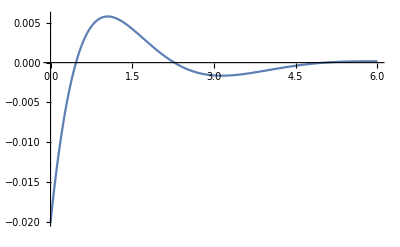

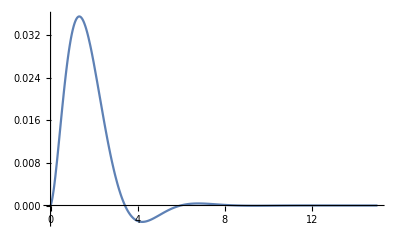

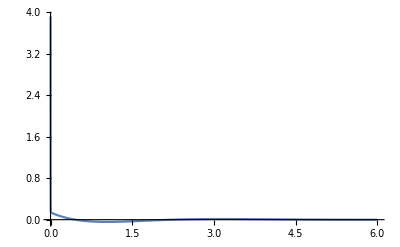

```mathematica
(*M=0.28;
m=0.46;
R=0.145;
g=9.81;
r=0.04;
*)
StaMod=StateSpaceModel[Eqns,{{x[t],0},{x'[t],0},{θ[t],0},{θ'[t],0}},{{F[t],0}},{},t]
gains=LQRegulatorGains[N[StaMod],{DiagonalMatrix[{400,1,3283,3283}],{{1}}}]//First
bumps[t_]=20Exp[-10(t-5)^2]-20Exp[-10(t-8)^2];
ctrlF=-gains.{x[t],x'[t],θ[t],θ'[t]}

errsum=Integrate[θ[t],t];
normF= -60θ[t]-0.5θ'[t]-100errsum
simu=NDSolve[Join[Eqns/.{F[t]->ctrlF},{x[0]==0,θ[0]==-0.02,x'[0]==0,θ'[0]==0}],{x,θ},{t,0,15}];
Plot[{θ[t]/.simu},{t,0,6},PlotRange->Full]
Plot[{x[t]/.simu},{t,0,15},PlotRange->Full]
coordT[th_]:={-R Sin[th],R Cos[th]};
coordX[t_]:={x[t]/.simu[[1]],r};
c[t_]:=coordT[θ[t]/.simu[[1]]]+coordX[t];
Plot[{ctrlF/.simu},{t,0,6},PlotRange->Full]
Animate[Show[Graphics[Line[{coordX[t],c[t]}]],Graphics[{PointSize[0.1],Point[c[t]]}],Graphics[{Circle[coordX[t],0.04]}],PlotRange->{{-0.2,0.2},{0,0.3}},AxesOrigin->{0,0},AxesLabel->{x,y},Axes->True],{t,0,15},AnimationRate->0.5]
```